NIntegrate::nlim: s = sigmaCL is not a valid limit of integration.

========= Final Results =========

A coefficient: 7.47×10^20 fb/(TeV⁻⁴)^2

95% CL upper limit on cross section σ_CL: 1.×10^3 fb

95% CL exclusion limit on f_M0 / Λ⁴: ±1.15×10^-9 TeV⁻⁴

=================================

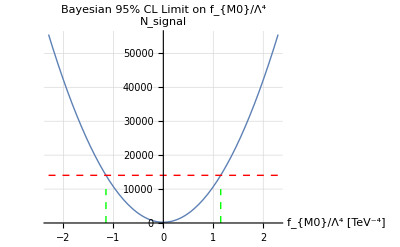

```mathematica
sigmaSM=15.38327;         (*Standard Model cross section in fb*)
sigmaFM0=0.0228501*1000;  (*Cross section at FM0_value*)
FM0value=100*10^-12;      (*FM0 input value in TeV^-4*)

L=100;                    (*Luminosity in fb^-1*)
effSignal=0.1405;         (*Signal efficiency*)
effBackground=0.1205;     (*Background efficiency*)
deltaSys=0.10;            (*Relative systematic uncertainty*)

(* ===A Coefficient from MadGraph samples===*)
A=(sigmaFM0-sigmaSM)/(FM0value^2);

(* ===Background event expectation and uncertainty===*)
NBackground=sigmaSM*effBackground*L;
deltaB=deltaSys*NBackground;

(* ===Poisson+Gaussian-Convolved Likelihood===*)
poissonGaussianLikelihood[nObs_,sigma_?NumericQ]:=Module[{S,integrand,bmin,bmax},S=sigma*effSignal*L;
integrand[b_]:=PDF[PoissonDistribution[nObs],S+b]*PDF[NormalDistribution[NBackground,deltaB],b];
bmin=Max[0,NBackground-5 deltaB];
bmax=NBackground+5 deltaB;
NIntegrate[integrand[b],{b,bmin,bmax},AccuracyGoal->6]];

(* ===Bayesian integration for 95% CL on σ===*)
bayesianCLLimit[nObs_,cl_]:=Module[{denominator,upperBound,func},upperBound=1000;(*fb*)denominator=NIntegrate[poissonGaussianLikelihood[nObs,s],{s,0,upperBound},AccuracyGoal->6];
func[sigmaCL_]:=NIntegrate[poissonGaussianLikelihood[nObs,s],{s,0,sigmaCL},AccuracyGoal->6]-cl*denominator;
sigmaCL/. FindRoot[func[sigmaCL],{sigmaCL,0.01,upperBound}]];

(* ===Solve for sigmaCL and limit on FM0===*)
nObs=Round[NBackground];
sigmaCL=bayesianCLLimit[nObs,0.95];

If[sigmaCL>sigmaSM,FM0limit=Sqrt[(sigmaCL-sigmaSM)/A],FM0limit=0];

Print["\n========= Final Results ========="];
Print["A coefficient: ",ScientificForm[A,3]," fb/(TeV⁻⁴)^2"];
Print["95% CL upper limit on cross section σ_CL: ",ScientificForm[sigmaCL,4]," fb"];
Print["95% CL exclusion limit on f_M0 / Λ⁴: ±",ScientificForm[FM0limit,3]," TeV⁻⁴"];
Print["=================================\n"];


(* ===Plot N_signal vs f_M0===*)
Plot[(sigmaSM+A f^2)*effSignal*L,{f,-2 FM0limit,2 FM0limit},PlotRange->All,AxesLabel->{"f_{M0}/Λ⁴ [TeV⁻⁴]","N_signal"},Epilog->{Red,Dashed,Line[{{-2 FM0limit,sigmaCL*effSignal*L},{2 FM0limit,sigmaCL*effSignal*L}}],Green,Dashed,Line[{{FM0limit,0},{FM0limit,10000}}],Green,Dashed,Line[{{-FM0limit,0},{-FM0limit,10000}}]},PlotLabel->"Bayesian 95% CL Limit on f_{M0}/Λ⁴",PlotStyle->Thick,GridLines->Automatic]
```